## Import data from txt files

#### Define the function that convert numbers to the format in file names

```mathematica
number2Printed[number_]:=Module[{returnedString="e",foo,bar,idx,oom},If[number==1,Return["1.0e+00"],If[number==0,Return["0.0e+00"],
If[number<1,
For[idx=1,StringLength[returnedString]==1,idx=idx+1,
foo=Floor[number/10^(-idx)];
If[foo==0,,
bar=Round[(number-foo*10^(-idx))/10^(-idx-1)];
If[StringLength[ToString[idx]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-0",ToString[idx]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-",ToString[idx]]
]
]
];
Return[returnedString]
,
oom=(StringLength[ToString[DecimalForm[Floor[number]*1.]]]-2);
foo=Floor[number/10^oom];
bar=Round[(number-foo*10^oom)/10^(oom-1)];
If[StringLength[ToString[oom]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+0",ToString[oom]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+",ToString[oom]]
];
Return[returnedString]
];
]
]
]
```

#### Import parameters

```mathematica
combinedParameters= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"combined_parameters.txt"]],{"["->"{","]"->"}"}]];
sequenceLengths= ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"sequence_lengths.txt"]],{"["->"{","]"->"}"}]];
populationSizes=  ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],"population_sizes.txt"]],{"["->"{","]"->"}"}]];
```

#### Import data

```mathematica
histograms=Table[Table[Table[Transpose[
ToExpression[StringReplace[Import[StringJoin[NotebookDirectory[],number2Printed[combinedParameters[[idx1]]],"_",number2Printed[sequenceLengths[[idx2]]],"_",number2Printed[populationSizes[[idx3]]],".txt"]],{"["->"{","]"->"}"}]]
],{idx3,Length[populationSizes]}],{idx2,Length[sequenceLengths]}],{idx1,Length[combinedParameters]}];
```

## Plot the comparisons

#### Define the predictions

```mathematica
simple[tau_,rho_]:=(2rho tau+1)Exp[-rho tau^2-tau]
complicated[tau_,rho_]:=(-rho Exp[-2tau]+rho+1)Exp[-rho/2*Exp[-2 tau]-(rho+1)tau+rho/2]
```

#### Generate the plots that verify parameter reduction

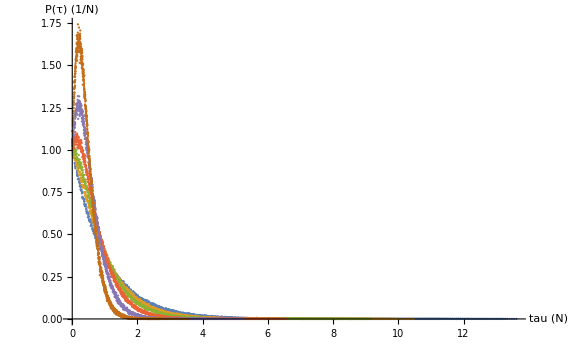
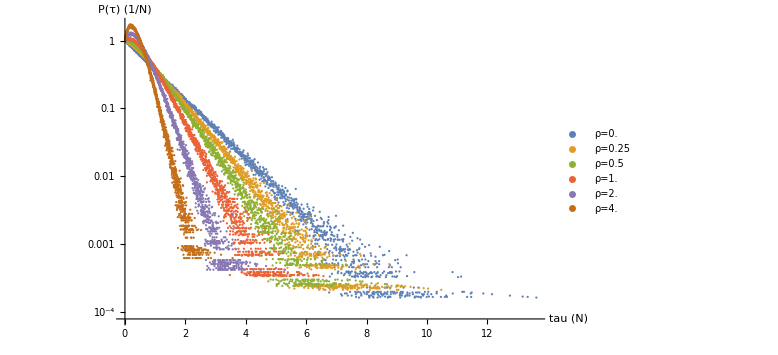

```mathematica
{ListPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,Ceiling[Length[combinedParameters]/2]}],ImageSize->Large,PlotRange->All,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"}],
ListLogPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,Ceiling[Length[combinedParameters]/2]}],ImageSize->Large,PlotRange->All,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"},PlotLegends->Table[StringJoin["ρ=",ToString[N[combinedParameters[[idx]]]]],{idx,Ceiling[Length[combinedParameters]/2]}]]}
```

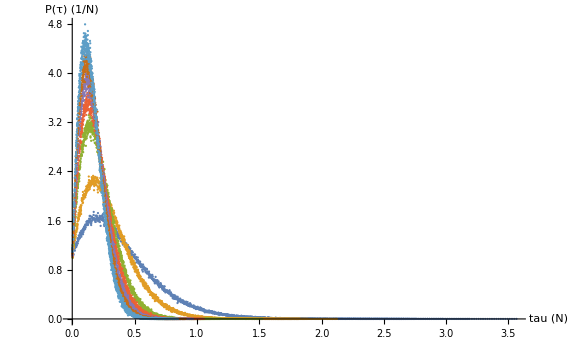
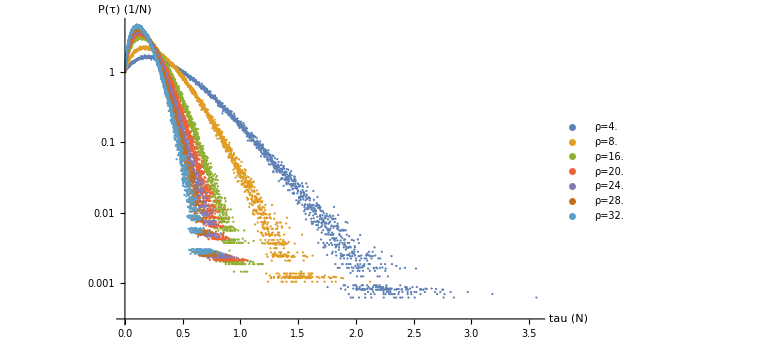

```mathematica
{ListPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,Floor[Length[combinedParameters]/2],Length[combinedParameters]}],ImageSize->Large,PlotRange->All,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"}],
ListLogPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,Floor[Length[combinedParameters]/2],Length[combinedParameters]}],ImageSize->Large,PlotRange->All,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"},PlotLegends->Table[StringJoin["ρ=",ToString[N[combinedParameters[[idx]]]]],{idx,Floor[Length[combinedParameters]/2],Length[combinedParameters]}]]}
```

#### Generate the regular and log plots for each of the 12 combined parameters to verify the predictions

General::munfl: 1.319155274396×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.427849716481×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.526662845649×10^-321 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

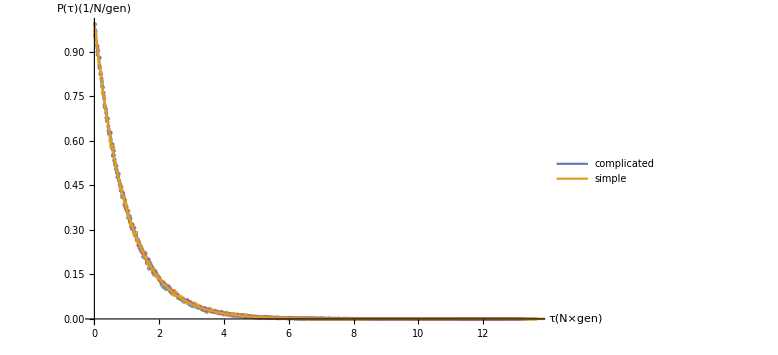
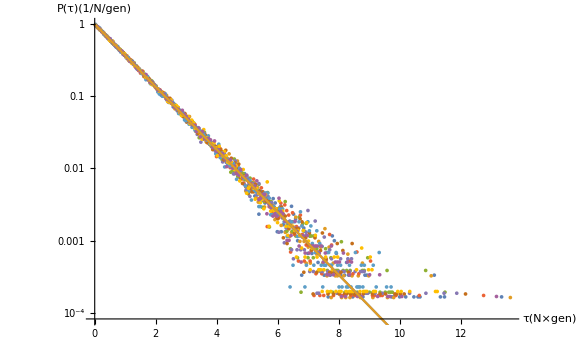
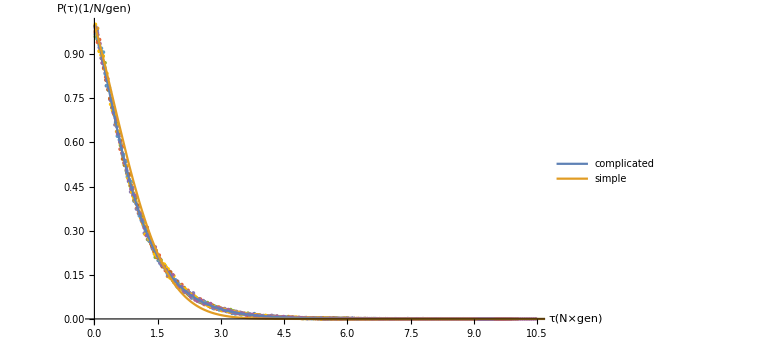
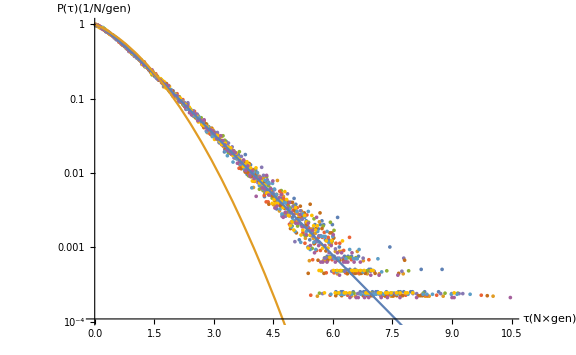
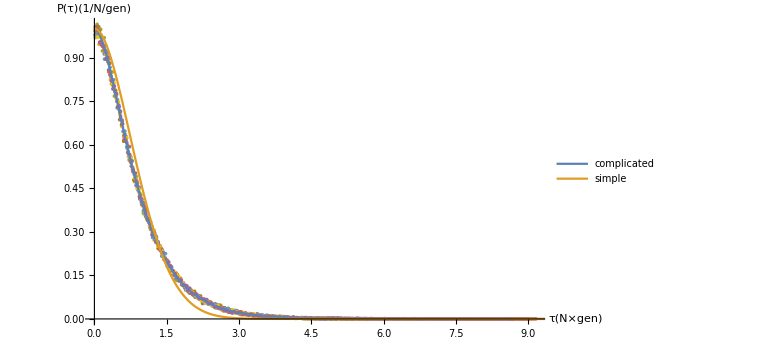
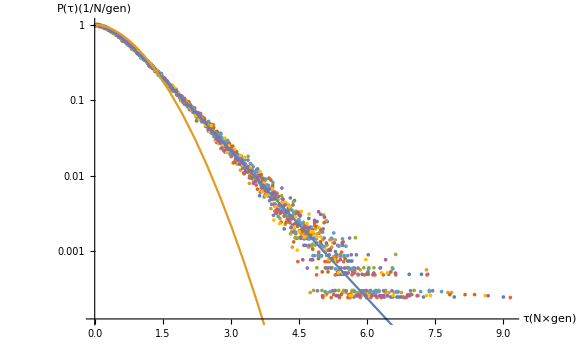
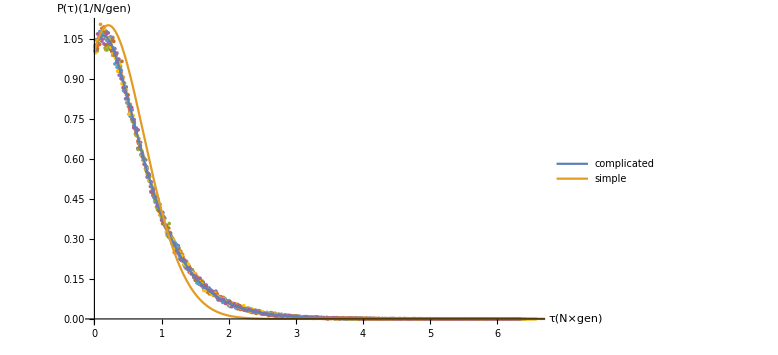
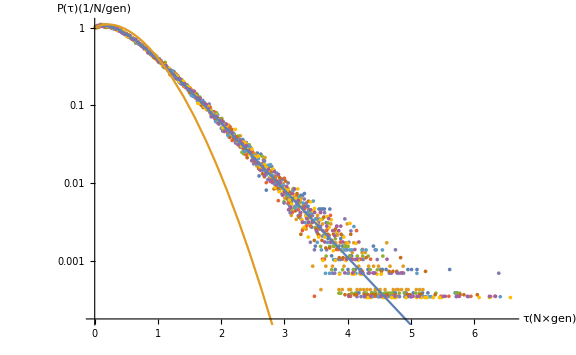
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
TableForm[Table[{
Show[
ListPlot[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],
ImageSize->Large,PlotRange->All,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"}],
Plot[{complicated[tau,combinedParameters[[idx0]]],simple[tau,combinedParameters[[idx0]]]},
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]*3/2},
PlotRange->Full,PlotStyle->Thick,PlotLegends->Placed[{"complicated","simple"},Below]]],
Show[
ListLogPlot[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],
ImageSize->Large,PlotRange->All,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"}],
LogPlot[{complicated[tau,combinedParameters[[idx0]]],simple[tau,combinedParameters[[idx0]]]},
{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]*3/2},
PlotRange->Full,PlotStyle->Thick,PlotLegends->Placed[StringJoin["ρ=",ToString[N[combinedParameters[[idx0]]]]],Bottom]]]},{idx0,Length[combinedParameters]}]]
```

#### Generate the 2 condensed plots in the report

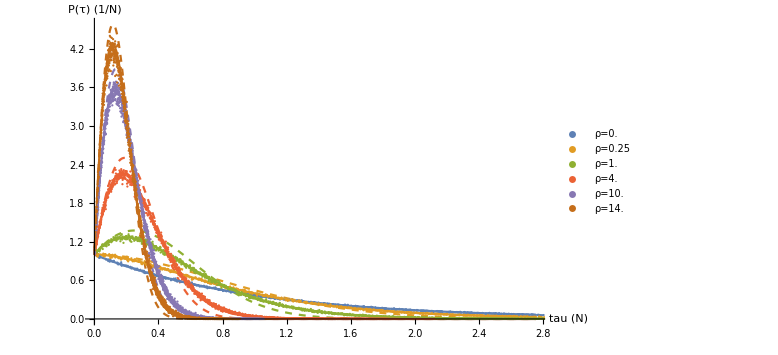

```mathematica
With[{complicatedPredictions=Table[complicated[tau,combinedParameters[[idx]]],{idx,1,Length[combinedParameters],2}],simplePredictions=Table[simple[tau,combinedParameters[[idx]]],{idx,1,Length[combinedParameters],2}]},Show[Plot[simplePredictions,{tau,0,Transpose[Max[histograms[[Floor[Length[combinedParameters]/2],1,1]]]][[1]]},PlotRange->Full,PlotStyle->Dashed,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"},ImageSize->Large],Plot[complicatedPredictions,{tau,0,Transpose[Max[histograms[[Floor[Length[combinedParameters]/2],1,1]]]][[1]]},PlotRange->Full,PlotStyle->Thick],ListPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,1,Length[combinedParameters],2}],PlotRange->All,PlotLegends->Table[StringJoin["ρ=",ToString[combinedParameters[[idx]]/2.]],{idx,1,Length[combinedParameters],2}]]]]
```

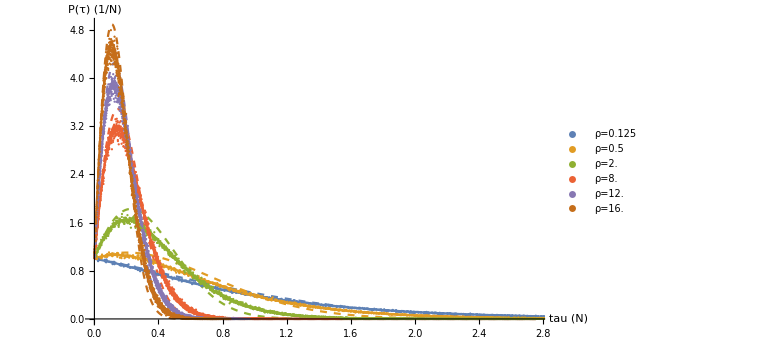

```mathematica
With[{complicatedPredictions=Table[complicated[tau,combinedParameters[[idx]]],{idx,2,Length[combinedParameters],2}],simplePredictions=Table[simple[tau,combinedParameters[[idx]]],{idx,2,Length[combinedParameters],2}]},Show[Plot[simplePredictions,{tau,0,Transpose[Max[histograms[[Floor[Length[combinedParameters]/2],1,1]]]][[1]]},PlotRange->Full,PlotStyle->Dashed,AxesLabel->{"tau\n(N)","P(τ)\n(1/N)"},ImageSize->Large],Plot[complicatedPredictions,{tau,0,Transpose[Max[histograms[[Floor[Length[combinedParameters]/2],1,1]]]][[1]]},PlotRange->Full,PlotStyle->Thick],ListPlot[Table[Flatten[Table[Table[histograms[[idx,idx1,idx2]],{idx2,3}],{idx1,3}],2],{idx,2,Length[combinedParameters],2}],PlotRange->All,PlotLegends->Table[StringJoin["ρ=",ToString[combinedParameters[[idx]]/2.]],{idx,2,Length[combinedParameters],2}]]]]
```